```mathematica
ClearAll["Global`*"]
```

```mathematica
(*solve with mathematica*)
```

```mathematica
(*u[x]_here = u_2[x]_notes*)
```

```mathematica
(*F_here =  F_{22}_notes*)
```

```mathematica
F[y_]:=1 + u'[y]
```

```mathematica
(*EE[x]_here  = E_22_notes*)
```

```mathematica
EE[y_]:=1/2(F[y]^2-1)
```

```mathematica
(*S[x]_here = S_{22}_notes*)
```

```mathematica
S[y_]:=(K+μ)EE[y]
```

```mathematica
(*P[x]_here  = P_{22}_notes*)
```

```mathematica
P[y_]:=F[y]S[y]
```

```mathematica
P[y]
```

1/2 (1.25+μ) (1+u'[y]) (-1+(1+u'[y])^2)

```mathematica
P[]
```

P[]

```mathematica
(*
The condition P[L]==0 has multiple solutions-> we pick the solution u'[L]==0
*)
```

```mathematica
L=1;
h=1;
K=1.25;
μ=1;
ρy[y_]:=1;
g=5/100;
```

```mathematica
sol=NDSolve[{P'[y]-ρy[y]g==0,u[0]==0,u'[-h]==0},u,{y,-h,0}][[1]]
```

{u→InterpolatingFunction[…]}

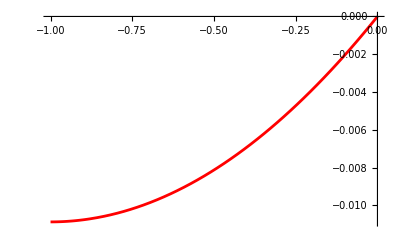

```mathematica
plotmathematica=Plot[u[y]/.sol,{y,-h,0},PlotStyle->Red]
```

```mathematica
(*import the solution with python*)
```

```mathematica
tab=Import["/Users/michelecastellana/Documents/finite_elements/elasticity/rod/steady_state/periodic/solution/u.csv"]
tab=Drop[tab,{1}]
```

```mathematica
(*here I substract h because the mesh has its bottom-left corner at the origin while in the analytical problem of a vertical rod in a gravitational field the bottom-left corner is at (0,-h)*)
```

```mathematica
tab=Table[{tab[[i,5]]-h,tab[[i,2]]},{i,1,Length[tab]}]
```

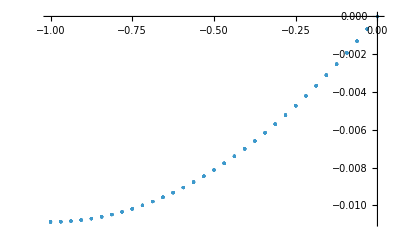

```mathematica
ListPlot[tab]
```

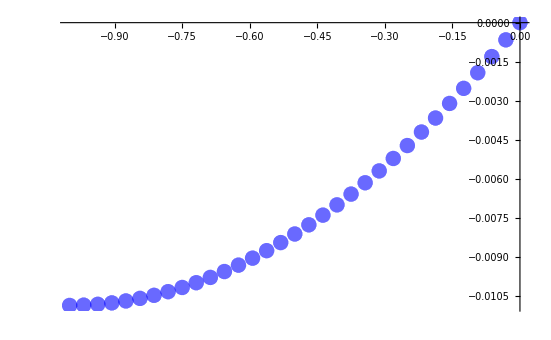

```mathematica
plotpython=ListPlot[tab,PlotStyle->{Blue, Opacity->0.05,PointSize->.02}]
```

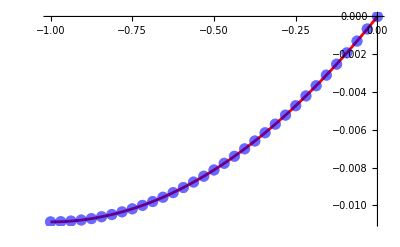

```mathematica
Show[plotmathematica,plotpython]
```